## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initialize Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "TALA2_param_inf";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Desktop/MD/kinetics/TALA2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;f6p,Null | 0.762 | 0.7239
0.8001 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009
Competitive | g3p | 0.000038
Competitive | f6p | 0.0012
Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0, 1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;f6p,Null | 0.762 | 0.7239
0.8001 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009
Competitive | g3p | 0.000038
Competitive | f6p | 0.0012
Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

```mathematica
inhibitionList
```

{{1,Kic,pi,0.019,{0.016,0.022},{},{{Competitive,e4p,0.00009},{Competitive,g3p,0.000038},{Competitive,f6p,0.0012},{Competitive,s7p,0.000285}},M,8.5,30,{{glygly,0.05}},{}}}

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[f6p,g3p,e4p,s7p]\""}}
```

```mathematica
catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                                      "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"]
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26}

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList,
						 otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{e4p^c→0,f6p^c→0}

{g3p^c→0,s7p^c→0}

{e4p^c→∞,f6p^c→∞}

{g3p^c→∞,s7p^c→∞}

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={{1,( Subscript[k, TALA21]^⟶/Subscript[k, TALA21]^⟵)*(Subscript[k, TALA22]^⟶/Subscript[k, TALA22]^⟵),7.33,{0.014, 3952}}};
customRatiosDataList
```

{{1,(k_TALA21^⟶ k_TALA22^⟶)/(k_TALA21^⟵ k_TALA22^⟵),7.33,{0.014,3952}}}

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.0166535,0.0166535,0.0166535,0.0166535}

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/haldaneRatio_1.txt"	0.762
1	0	0	3.7999999999999996e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.86319311139679
1	0.0009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.9090909090909093
1	0.01	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.09090909090909088
1	0.01	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.13680688860321
1	0.01	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.20076000891310164
1	0.01	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.28474724895080133
1	0.01	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.38686317984685703
1	0.01	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.49999999999999994
1	0.01	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.613136820153143
1	0.01	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.7152527510491984
1	0.01	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.7992399910868982
1	0.01	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.8631931113967899
1	0.01	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.9090909090909092
1	0	0	0.01	0.0000285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.09090909090909093
1	0	0	0.01	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.13680688860321005
1	0	0	0.01	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.2007600089131019
1	0	0	0.01	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.28474724895080145
1	0	0	0.01	0.000179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.38686317984685686
1	0	0	0.01	0.000285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.5
1	0	0	0.01	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.6131368201531432
1	0	0	0.01	0.000715887632980231	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.7152527510491988
1	0	0	0.01	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.7992399910868982
1	0	0	0.01	0.00179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.86319311139679
1	0	0	0.01	0.00285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.9090909090909091
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	71.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/absRateFor.txt"	79.4
1	9.000000000000007e-6	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.612574113277207
1	0.0009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_e4p.txt"	0.7692307692307694
1	0	0	3.7999999999999996e-6	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_g3p.txt"	0.7692307692307692
1	0.01	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.06249999999999998
1	0.01	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.1741123948954683
1	0.01	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.3999999999999999
1	0.01	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.6782688399674104
1	0.01	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.8695652173913043
1	0.01	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.0476190476190476
1	0.01	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.13652705949581428
1	0.01	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.33333333333333326
1	0.01	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.6125741132772069
1	0.01	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.8333333333333333
1	0.01	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.03225806451612902
1	0.01	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.09535767393825996
1	0.01	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.2499999999999999
1	0.01	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.513167019494862
1	0.01	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateFor_f6p.txt"	0.769230769230769
1	0	0	0.01	0.0000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.06250000000000001
1	0	0	0.01	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.17411239489546834
1	0	0	0.01	0.000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.39999999999999997
1	0	0	0.01	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.6782688399674105
1	0	0	0.01	0.00285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.8695652173913043
1	0	0	0.01	0.0000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.04761904761904762
1	0	0	0.01	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.13652705949581434
1	0	0	0.01	0.000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.3333333333333333
1	0	0	0.01	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.6125741132772069
1	0	0	0.01	0.00285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.8333333333333333
1	0	0	0.01	0.0000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.03225806451612904
1	0	0	0.01	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.09535767393825997
1	0	0	0.01	0.000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.25
1	0	0	0.01	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.513167019494862
1	0	0	0.01	0.00285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/relRateRev_s7p.txt"	0.7692307692307693
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_inf/input/customRatio_1.txt"	7.33

#### sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];
```

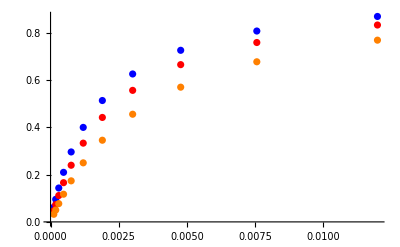

```mathematica
inhib1=inhibFittingData[[1;;11,{3,-1}]];
inhib2=inhibFittingData[[12;;22,{3,-1}]];
inhib3=inhibFittingData[[23;;33,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0018}

{1.,0.0024}

{1.,0.0036}

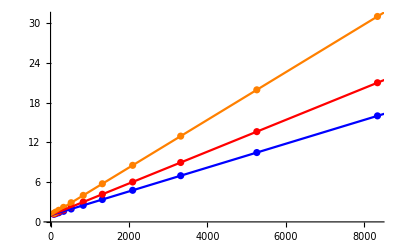

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,10000}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
Dimensions@allFittingData
```

{192,11}

### Simulate data with uncertainty

```mathematica
Export["TALA2SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TALA2SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList,  customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

```mathematica
FilePrint[dataPathList[[1]]]
```

e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	3.4971596682114973e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909086
0	0	5.542624551097971e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860320997
0	0	8.784467919403012e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310178
0	0	0.000013922443404854854	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.28474724895080117
0	0	0.000022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
0	0	0.00003497159668211497	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.4999999999999998
0	0	0.00005542624551097971	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.613136820153143
0	0	0.00008784467919403013	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491986
0	0	0.00013922443404854867	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868981
0	0	0.00022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.8631931113967898
0	0	0.00034971596682114973	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
0.000010205108679489661	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909094
0.000016174007274448992	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.1368068886032101
0.000025634074024090747	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310192
0.000040627269415825704	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508017
0.00006438988272542566	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.386863179846857
0.0001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5
0.00016174007274448994	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.0002563407402409075	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.00040627269415825665	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868984
0.0006438988272542565	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909092
0.01	0.00012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.0909090909090909
0.01	0.00019117773077797782	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321003
0.01	0.00030299628406018036	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.2007600089131017
0.01	0.0004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080145
0.01	0.0007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685686
0.01	0.0012062499333542213	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.4999999999999999
0.01	0.0019117773077797781	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.6131368201531431
0.01	0.0030299628406018067	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491987
0.01	0.004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
0.01	0.007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
0.01	0.012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909091
0	0	0.01	0.000028550945785075704	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.0909090909090909
0	0	0.01	0.00004525019961309282	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0	0	0.01	0.00007171673332429735	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.20076000891310186
0	0	0.01	0.00011366336243122789	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0	0	0.01	0.00018014428934949323	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.3868631798468568
0	0	0.01	0.000285509457850757	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.4999999999999999
0	0	0.01	0.00045250199613092824	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531431
0	0	0.01	0.0007171673332429736	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0	0	0.01	0.001136633624312279	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868984
0	0	0.01	0.0018014428934949324	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.8631931113967899
0	0	0.01	0.0028550945785075703	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909092
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.00011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06249999999999998
0.01	0.00037947331922020535	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1741123948954683
0.01	0.0011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.3999999999999999
0.01	0.003794733192202054	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674104
0.01	0.011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
0.01	0.00011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.0476190476190476
0.01	0.00037947331922020535	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.13652705949581428
0.01	0.0011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333326
0.01	0.003794733192202054	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6125741132772069
0.01	0.011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333333
0.01	0.00011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612902
0.01	0.00037947331922020535	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393825996
0.01	0.0011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.2499999999999999
0.01	0.003794733192202054	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.513167019494862
0.01	0.011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.769230769230769
9.000000000000007e-6	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06250000000000004
0.000028460498941515435	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.17411239489546843
0.00009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.40000000000000013
0.00028460498941515434	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674106
0.0009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
9.000000000000007e-6	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.04761904761904766
0.000028460498941515435	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1365270594958144
0.00009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333354
0.00028460498941515434	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.612574113277207
0.0009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333336
9.000000000000007e-6	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612906
0.000028460498941515435	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393826003
0.00009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.25000000000000017
0.00028460498941515434	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.5131670194948621
0.0009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.7692307692307694
0	0	0.01	0.0000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.06250000000000001
0	0	0.01	0.00009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.01	0.000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.39999999999999997
0	0	0.01	0.0009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.01	0.00285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	0.01	0.0000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904762
0	0	0.01	0.00009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.13652705949581434
0	0	0.01	0.000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3333333333333333
0	0	0.01	0.0009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772069
0	0	0.01	0.00285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333333
0	0	0.01	0.0000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.03225806451612904
0	0	0.01	0.00009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.01	0.000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.25
0	0	0.01	0.0009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.513167019494862
0	0	0.01	0.00285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307693
0	0	3.7999999999999996e-6	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.062499999999999986
0	0	0.000012016655108639841	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.000037999999999999995	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3999999999999999
0	0	0.0001201665510863984	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.00037999999999999997	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	3.7999999999999996e-6	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904761
0	0	0.000012016655108639841	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.1365270594958143
0	0	0.000037999999999999995	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.33333333333333326
0	0	0.0001201665510863984	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772068
0	0	0.00037999999999999997	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333334
0	0	3.7999999999999996e-6	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.032258064516129024
0	0	0.000012016655108639841	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.000037999999999999995	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.24999999999999997
0	0	0.0001201665510863984	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.5131670194948619
0	0	0.00037999999999999997	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307692
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

### Parameter influence

```mathematica
dataFileName = "TALA2_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_Km1";
KeqListTemp=KeqList;
kmListTemp=kmList[[2;;]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];


dataFileName = "TALA2_Km2";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[3]], kmList[[4]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];


dataFileName = "TALA2_Km3";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[2]], kmList[[4]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_Km4";
KeqListTemp=KeqList;
kmListTemp=kmList[[;;3]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "TALA2_Ki";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = {};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Part::partw: Part 1 of {} does not exist.

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating custom ratios data...

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  7.33,10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

```mathematica
FilePrint[dataPathList[[15]]]
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/haldaneRatio_1.txt"	0.762
1	0	0	3.7999999999999996e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	0.01	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.86319311139679
1	0.0009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.9090909090909093
1	0.01	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.09090909090909088
1	0.01	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.13680688860321
1	0.01	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.20076000891310164
1	0.01	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.28474724895080133
1	0.01	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.38686317984685703
1	0.01	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.49999999999999994
1	0.01	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.613136820153143
1	0.01	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.7152527510491984
1	0.01	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.7992399910868982
1	0.01	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.8631931113967899
1	0.01	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.9090909090909092
1	0	0	0.01	0.0000285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.09090909090909093
1	0	0	0.01	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.13680688860321005
1	0	0	0.01	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.2007600089131019
1	0	0	0.01	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.28474724895080145
1	0	0	0.01	0.000179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.38686317984685686
1	0	0	0.01	0.000285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.5
1	0	0	0.01	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.6131368201531432
1	0	0	0.01	0.000715887632980231	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.7152527510491988
1	0	0	0.01	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.7992399910868982
1	0	0	0.01	0.00179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.86319311139679
1	0	0	0.01	0.00285	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.9090909090909091
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	71.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/absRateFor.txt"	79.4
1	9.000000000000007e-6	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.612574113277207
1	0.0009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_e4p.txt"	0.7692307692307694
1	0	0	3.7999999999999996e-6	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	0.01	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	0.01	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	0.01	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_g3p.txt"	0.7692307692307692
1	0.01	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.06249999999999998
1	0.01	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.1741123948954683
1	0.01	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.3999999999999999
1	0.01	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.6782688399674104
1	0.01	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.8695652173913043
1	0.01	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.0476190476190476
1	0.01	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.13652705949581428
1	0.01	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.33333333333333326
1	0.01	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.6125741132772069
1	0.01	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.8333333333333333
1	0.01	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.03225806451612902
1	0.01	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.09535767393825996
1	0.01	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.2499999999999999
1	0.01	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.513167019494862
1	0.01	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateFor_f6p.txt"	0.769230769230769
1	0	0	0.01	0.0000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.06250000000000001
1	0	0	0.01	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.17411239489546834
1	0	0	0.01	0.000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.39999999999999997
1	0	0	0.01	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.6782688399674105
1	0	0	0.01	0.00285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.8695652173913043
1	0	0	0.01	0.0000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.04761904761904762
1	0	0	0.01	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.13652705949581434
1	0	0	0.01	0.000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.3333333333333333
1	0	0	0.01	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.6125741132772069
1	0	0	0.01	0.00285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.8333333333333333
1	0	0	0.01	0.0000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.03225806451612904
1	0	0	0.01	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.09535767393825997
1	0	0	0.01	0.000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.25
1	0	0	0.01	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.513167019494862
1	0	0	0.01	0.00285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/relRateRev_s7p.txt"	0.7692307692307693
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/input/customRatio_1.txt"	10.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 23.470101427
best_fit: 11.6955688566
best_fit: 11.7455238246
best_fit: 1.09096367255
best_fit: 11.696370409
best_fit: 0.995585266542
best_fit: 0.986558286933
best_fit: 0.97525579843
best_fit: 1.05995186441
best_fit: 1.03452273433
best_fit: 1.08240803226
best_fit: 0.528833078663
best_fit: 12.5269732438
best_fit: 19.9183804591
best_fit: 11.6861198687
best_fit: 1.00117334878
best_fit: 1.66609754408
best_fit: 1.0978147682
best_fit: 1.01403243846
best_fit: 1.08064850405

## Pull in Parameters and Check Fit and Enzyme Statistics for param_scan

```mathematica
outputPath
```

/home/mrama/Desktop/MD/kinetics/TALA2/TALA2_param_scan/output

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  7.33,10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

nEnsembles = 10;

flagFitType = "abs_ssd";
errorList = {};
Do[
Do[
fitDescription = paramScan[[1]] <>"_"<>ToString[paramScan[[2]]]<>"_"<> ToString[N@AccountingForm[paramVal]];

ssdList = 
Table[

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> "_"<>ToString@ensembleI<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "TALA2_"<> fitDescription<>".dat"}, OperatingSystem->$OperatingSystem];


{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];
Print@{paramVal, filteredDataList[[1,1]]};
ToString[N@AccountingForm[filteredDataList[[1,1]]]],

{ensembleI, Range[nEnsembles]}];

Print[ssdList];
AppendTo[errorList, Flatten@{ToString[N@AccountingForm[paramVal]], ssdList}];,

{paramVal, paramScan[[3]]}];,
{paramScan, paramScanList}];

Export[ FileNameJoin[{outputPath, "treated_data", "param_scan_ssd.csv"}, OperatingSystem->$OperatingSystem],errorList, "TSV"];
```

```mathematica
errorList//TableForm
```

customRatio_1 | 0.000000000001 | 0.00000000102726
customRatio_1 | 0.00000000001 | 0.00000000042135
customRatio_1 | 0.0000000001 | 0.0000000000102364
customRatio_1 | 0.000000001 | 0.0000000000066693
customRatio_1 | 0.00000001 | 0.00000000000145757
customRatio_1 | 0.0000001 | 0.00000000000344528
customRatio_1 | 0.000001 | 0.00000000000166854
customRatio_1 | 0.00000109 | 0.00000000000443924
customRatio_1 | 0.00001 | 0.000000000000105293
customRatio_1 | 0.0001 | 0.0000000000000000000461147
customRatio_1 | 0.001 | 0.0000000000000000162621
customRatio_1 | 0.01 | 0.00000000000000245293
customRatio_1 | 0.1 | 0.0000000000000000243629
customRatio_1 | 1. | 0.00000000000000000325224
customRatio_1 | 10. | 0.00000000000000000593573
customRatio_1 | 100. | 0.000000000000000197496
customRatio_1 | 1000. | 0.311466
customRatio_1 | 10000. | 5.99475
customRatio_1 | 100000. | 493.835
customRatio_1 | 1000000. | 47447.5
customRatio_1 | 10000000. | 657266.
customRatio_1 | 100000000. | 788019.
customRatio_1 | 1000000000. | 790041.
customRatio_1 | 10000000000. | 790071.
customRatio_1 | 100000000000. | 790072.
customRatio_1 | 1000000000000. | 790074.

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | relRateFor_nad | 1.04138 | 1.08448 | 0.909065 | 999.972 | 0.0909091 | 0.999974
1 | relRateFor_nad | 0.863885 | 0.746297 | 0.863177 | 630.946 | 0.136807 | 0.999984
1 | relRateFor_nad | 0.697318 | 0.486253 | 0.79923 | 398.102 | 0.20076 | 0.99999
1 | relRateFor_nad | 0.545538 | 0.297611 | 0.715246 | 251.186 | 0.284747 | 0.999994
1 | relRateFor_nad | 0.412441 | 0.170107 | 0.613133 | 158.488 | 0.386863 | 0.999996
1 | relRateFor_nad | 0.301029 | 0.0906184 | 0.499997 | 99.9995 | 0.5 | 0.999997
1 | relRateFor_nad | 0.212442 | 0.0451316 | 0.386862 | 63.0955 | 0.613137 | 0.999998
1 | relRateFor_nad | 0.14554 | 0.0211819 | 0.284746 | 39.8106 | 0.715253 | 0.999999
1 | relRateFor_nad | 0.0973225 | 0.00947167 | 0.200759 | 25.1188 | 0.79924 | 0.999999
1 | relRateFor_nad | 0.0638919 | 0.00408217 | 0.136806 | 15.8489 | 0.863193 | 1.
1 | relRateFor_nad | 0.0413926 | 0.00171335 | 0.0909088 | 9.99997 | 0.909091 | 1.
1 | relRateFor_g3p | 0.43838 | 0.192177 | 0.158543 | 174.398 | 0.0909091 | 0.249452
1 | relRateFor_g3p | 0.401732 | 0.161388 | 0.208209 | 152.192 | 0.136807 | 0.345016
1 | relRateFor_g3p | 0.355331 | 0.12626 | 0.254237 | 126.637 | 0.20076 | 0.454997
1 | relRateFor_g3p | 0.301072 | 0.0906446 | 0.284803 | 100.02 | 0.284747 | 0.56955
1 | relRateFor_g3p | 0.243103 | 0.0590992 | 0.290249 | 75.0263 | 0.386863 | 0.677112
1 | relRateFor_g3p | 0.186793 | 0.0348918 | 0.268711 | 53.7423 | 0.5 | 0.768711
1 | relRateFor_g3p | 0.136954 | 0.0187563 | 0.227311 | 37.0735 | 0.613137 | 0.840448
1 | relRateFor_g3p | 0.0964071 | 0.00929432 | 0.177778 | 24.8553 | 0.715253 | 0.893031
1 | relRateFor_g3p | 0.0656812 | 0.00431402 | 0.130493 | 16.3272 | 0.79924 | 0.929733
1 | relRateFor_g3p | 0.0436609 | 0.00190627 | 0.0912914 | 10.576 | 0.863193 | 0.954484
1 | relRateFor_g3p | 0.0285184 | 0.000813301 | 0.0617001 | 6.78701 | 0.909091 | 0.970791
1 | relRateFor_pi | 17.4074 | 303.019 | 0.0909091 | 100. | 0.0909091 | 3.55764×10^-19
1 | relRateFor_pi | 17.3849 | 302.236 | 0.136807 | 100. | 0.136807 | 5.63848×10^-19
1 | relRateFor_pi | 17.3515 | 301.075 | 0.20076 | 100. | 0.20076 | 8.9364×10^-19
1 | relRateFor_pi | 17.3033 | 299.404 | 0.284747 | 100. | 0.284747 | 1.41632×10^-18
1 | relRateFor_pi | 17.2364 | 297.093 | 0.386863 | 100. | 0.386863 | 2.24472×10^-18
1 | relRateFor_pi | 17.1478 | 294.047 | 0.5 | 100. | 0.5 | 3.55764×10^-18
1 | relRateFor_pi | 17.0364 | 290.239 | 0.613137 | 100. | 0.613137 | 5.63848×10^-18
1 | relRateFor_pi | 16.9033 | 285.721 | 0.715253 | 100. | 0.715253 | 8.9364×10^-18
1 | relRateFor_pi | 16.7515 | 280.613 | 0.79924 | 100. | 0.79924 | 1.41632×10^-17
1 | relRateFor_pi | 16.5849 | 275.06 | 0.863193 | 100. | 0.863193 | 2.24472×10^-17
1 | relRateFor_pi | 16.4074 | 269.204 | 0.909091 | 100. | 0.909091 | 3.55764×10^-17
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12

### Simulated Data and Best Fit Data Plot

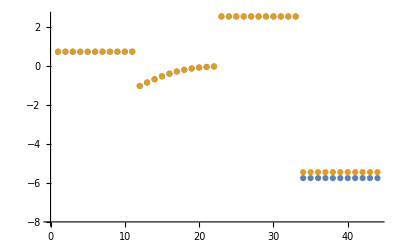

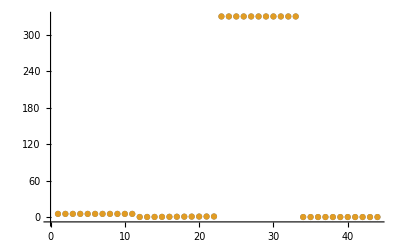

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics for param_inf

```mathematica
paramList={"all", "dKd", "kcat", "Keq", "Km1", "Km2", "Km3", "Km4", "Ki"};
nEnsembles = 99;

flagFitType = "abs_ssd";

Do[
Do[

fitDescription = param <>"_"<>ToString[fitI];

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "TALA2_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];,

{fitI, 0, nEnsembles}],
{param, paramList}];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | relRateFor_2pg | 4.72843×10^-7 | 2.2358×10^-13 | 9.89783×10^-8 | 0.000108876 | 0.0909091 | 0.0909092
1 | relRateFor_2pg | 4.4897×10^-7 | 2.01574×10^-13 | 1.4143×10^-7 | 0.000103379 | 0.136807 | 0.136807
1 | relRateFor_2pg | 4.15706×10^-7 | 1.72812×10^-13 | 1.92167×10^-7 | 0.00009572 | 0.20076 | 0.20076
1 | relRateFor_2pg | 3.72022×10^-7 | 1.38401×10^-13 | 2.43918×10^-7 | 0.0000856614 | 0.284747 | 0.284747
1 | relRateFor_2pg | 3.18909×10^-7 | 1.01703×10^-13 | 2.8408×10^-7 | 0.0000734316 | 0.386863 | 0.386863
1 | relRateFor_2pg | 2.60064×10^-7 | 6.76331×10^-14 | 2.99409×10^-7 | 0.0000598819 | 0.5 | 0.5
1 | relRateFor_2pg | 2.01218×10^-7 | 4.04887×10^-14 | 2.8408×10^-7 | 0.0000463322 | 0.613137 | 0.613137
1 | relRateFor_2pg | 1.48105×10^-7 | 2.1935×10^-14 | 2.43918×10^-7 | 0.0000341024 | 0.715253 | 0.715253
1 | relRateFor_2pg | 1.04421×10^-7 | 1.09037×10^-14 | 1.92167×10^-7 | 0.0000240438 | 0.79924 | 0.79924
1 | relRateFor_2pg | 7.1157×10^-8 | 5.06331×10^-15 | 1.4143×10^-7 | 0.0000163845 | 0.863193 | 0.863193
1 | relRateFor_2pg | 4.72843×10^-8 | 2.2358×10^-15 | 9.89782×10^-8 | 0.0000108876 | 0.909091 | 0.909091
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6

### Simulated Data and Best Fit Data Plot

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

-Graphics-

-Graphics-

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
param = "dKd";
fitDescription= param <>"_1";

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "TALA2_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
Length@Select[filteredDataList[[All,1]], #<= 1&]
```

72

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | haldaneRatio_1 | 1.24466×10^-8 | 1.54918×10^-16 | 2.18384×10^-8 | 2.86594×10^-6 | 0.762 | 0.762
1 | relRateRev_g3p | 0.0106316 | 0.000113032 | 0.00225294 | 2.47823 | 0.0909091 | 0.093162
1 | relRateRev_g3p | 0.0100886 | 0.000101779 | 0.0032152 | 2.35017 | 0.136807 | 0.140022
1 | relRateRev_g3p | 0.00933303 | 0.0000871055 | 0.00436105 | 2.17227 | 0.20076 | 0.205121
1 | relRateRev_g3p | 0.0083428 | 0.0000696023 | 0.00552287 | 1.93957 | 0.284747 | 0.29027
1 | relRateRev_g3p | 0.00714185 | 0.0000510061 | 0.00641446 | 1.65807 | 0.386863 | 0.393278
1 | relRateRev_g3p | 0.00581516 | 0.0000338161 | 0.00673998 | 1.348 | 0.5 | 0.50674
1 | relRateRev_g3p | 0.00449251 | 0.0000201827 | 0.00637544 | 1.03981 | 0.613137 | 0.619512
1 | relRateRev_g3p | 0.00330215 | 0.0000109042 | 0.00545914 | 0.763247 | 0.715253 | 0.720712
1 | relRateRev_g3p | 0.00232556 | 5.40821×10^-6 | 0.00429124 | 0.536915 | 0.79924 | 0.803531
1 | relRateRev_g3p | 0.00158339 | 2.50711×10^-6 | 0.00315284 | 0.365254 | 0.863193 | 0.866346
1 | relRateRev_g3p | 0.00105153 | 1.10571×10^-6 | 0.00220379 | 0.242416 | 0.909091 | 0.911295
1 | relRateFor_e4p | 0.00781035 | 0.0000610016 | 0.0016203 | 1.78233 | 0.0909091 | 0.0892888
1 | relRateFor_e4p | 0.00741938 | 0.0000550472 | 0.00231732 | 1.69386 | 0.136807 | 0.13449
1 | relRateFor_e4p | 0.00687401 | 0.000047252 | 0.00315261 | 1.57034 | 0.20076 | 0.197607
1 | relRateFor_e4p | 0.00615676 | 0.0000379057 | 0.00400823 | 1.40764 | 0.284747 | 0.280739
1 | relRateFor_e4p | 0.00528309 | 0.000027911 | 0.00467759 | 1.20911 | 0.386863 | 0.382186
1 | relRateFor_e4p | 0.00431307 | 0.0000186025 | 0.00494103 | 0.988205 | 0.5 | 0.495059
1 | relRateFor_e4p | 0.00334088 | 0.0000111615 | 0.00469855 | 0.766314 | 0.613137 | 0.608438
1 | relRateFor_e4p | 0.00246152 | 6.05906×10^-6 | 0.00404248 | 0.565182 | 0.715253 | 0.71121
1 | relRateFor_e4p | 0.00173693 | 3.01693×10^-6 | 0.00319012 | 0.399145 | 0.79924 | 0.79605
1 | relRateFor_e4p | 0.00118438 | 1.40275×10^-6 | 0.00235083 | 0.272341 | 0.863193 | 0.860842
1 | relRateFor_e4p | 0.000787387 | 6.19978×10^-7 | 0.00164671 | 0.181138 | 0.909091 | 0.907444
1 | relRateFor_f6p | 0.000916905 | 8.40715×10^-7 | 0.00019173 | 0.210903 | 0.0909091 | 0.0907174
1 | relRateFor_f6p | 0.000870659 | 7.58048×10^-7 | 0.000273991 | 0.200276 | 0.136807 | 0.136533
1 | relRateFor_f6p | 0.000806213 | 6.49979×10^-7 | 0.00037234 | 0.185465 | 0.20076 | 0.200388
1 | relRateFor_f6p | 0.000721563 | 5.20653×10^-7 | 0.000472704 | 0.166008 | 0.284747 | 0.284275
1 | relRateFor_f6p | 0.00061862 | 3.8269×10^-7 | 0.000550665 | 0.142341 | 0.386863 | 0.386313
1 | relRateFor_f6p | 0.000504537 | 2.54558×10^-7 | 0.000580533 | 0.116107 | 0.5 | 0.499419
1 | relRateFor_f6p | 0.000390425 | 1.52432×10^-7 | 0.000550954 | 0.0898583 | 0.613137 | 0.612586
1 | relRateFor_f6p | 0.000287403 | 8.26006×10^-8 | 0.000473176 | 0.0661551 | 0.715253 | 0.71478
1 | relRateFor_f6p | 0.000202652 | 4.1068×10^-8 | 0.000372858 | 0.0466515 | 0.79924 | 0.798867
1 | relRateFor_f6p | 0.000138107 | 1.90734×10^-8 | 0.000274454 | 0.0317952 | 0.863193 | 0.862919
1 | relRateFor_f6p | 0.0000917777 | 8.42314×10^-9 | 0.000192094 | 0.0211304 | 0.909091 | 0.908899
1 | relRateRev_s7p | 0.0000211664 | 4.48016×10^-10 | 4.43078×10^-6 | 0.00487386 | 0.0909091 | 0.0909135
1 | relRateRev_s7p | 0.0000200977 | 4.03918×10^-10 | 6.33112×10^-6 | 0.00462778 | 0.136807 | 0.136813
1 | relRateRev_s7p | 0.0000186087 | 3.46282×10^-10 | 8.60236×10^-6 | 0.0042849 | 0.20076 | 0.200769
1 | relRateRev_s7p | 0.0000166532 | 2.77328×10^-10 | 0.0000109189 | 0.0038346 | 0.284747 | 0.284758
1 | relRateRev_s7p | 0.0000142756 | 2.03792×10^-10 | 0.0000127167 | 0.00328712 | 0.386863 | 0.386876
1 | relRateRev_s7p | 0.0000116414 | 1.35522×10^-10 | 0.0000134028 | 0.00268056 | 0.5 | 0.500013
1 | relRateRev_s7p | 9.00722×10^-6 | 8.113×10^-11 | 0.0000127165 | 0.00207401 | 0.613137 | 0.61315
1 | relRateRev_s7p | 6.62967×10^-6 | 4.39525×10^-11 | 0.0000109187 | 0.00152655 | 0.715253 | 0.715264
1 | relRateRev_s7p | 4.67421×10^-6 | 2.18482×10^-11 | 8.60208×10^-6 | 0.00107628 | 0.79924 | 0.799249
1 | relRateRev_s7p | 3.18521×10^-6 | 1.01456×10^-11 | 6.33087×10^-6 | 0.000733425 | 0.863193 | 0.863199
1 | relRateRev_s7p | 2.11659×10^-6 | 4.47996×10^-12 | 4.43059×10^-6 | 0.000487364 | 0.909091 | 0.909095
1 | relRateFor_e4p | 0.00886199 | 0.0000785349 | 0.00126242 | 2.01987 | 0.0625 | 0.0612376
1 | relRateFor_e4p | 0.00781638 | 0.0000610958 | 0.00310562 | 1.78369 | 0.174112 | 0.171007
1 | relRateFor_e4p | 0.00569247 | 0.0000324042 | 0.00520874 | 1.30219 | 0.4 | 0.394791
1 | relRateFor_e4p | 0.00306168 | 9.37389×10^-6 | 0.00476483 | 0.702499 | 0.678269 | 0.673504
1 | relRateFor_e4p | 0.00124386 | 1.54718×10^-6 | 0.00248694 | 0.285999 | 0.869565 | 0.867078
1 | relRateFor_e4p | 0.000970752 | 9.4236×10^-7 | 0.000106559 | 0.223774 | 0.047619 | 0.0477256
1 | relRateFor_e4p | 0.000880037 | 7.74466×10^-7 | 0.000276934 | 0.202842 | 0.136527 | 0.136804
1 | relRateFor_e4p | 0.000679299 | 4.61447×10^-7 | 0.000521789 | 0.156537 | 0.333333 | 0.333855
1 | relRateFor_e4p | 0.000394638 | 1.55739×10^-7 | 0.000556891 | 0.0909099 | 0.612574 | 0.613131
1 | relRateFor_e4p | 0.000169725 | 2.88066×10^-8 | 0.000325736 | 0.0390883 | 0.833333 | 0.833659
1 | relRateFor_e4p | 0.0296782 | 0.000880795 | 0.00228147 | 7.07256 | 0.0322581 | 0.0345395
1 | relRateFor_e4p | 0.02768 | 0.000766185 | 0.00627555 | 6.58106 | 0.0953577 | 0.101633
1 | relRateFor_e4p | 0.0228216 | 0.000520824 | 0.0134884 | 5.39538 | 0.25 | 0.263488
1 | relRateFor_e4p | 0.0146764 | 0.000215398 | 0.0176382 | 3.43713 | 0.513167 | 0.530805
1 | relRateFor_e4p | 0.00689516 | 0.0000475432 | 0.0123103 | 1.60034 | 0.769231 | 0.781541
1 | relRateRev_g3p | 0.00587646 | 0.0000345328 | 0.000839995 | 1.34399 | 0.0625 | 0.06166
1 | relRateRev_g3p | 0.00518101 | 0.0000268428 | 0.00206477 | 1.18588 | 0.174112 | 0.172048
1 | relRateRev_g3p | 0.00377009 | 0.0000142135 | 0.00345735 | 0.864337 | 0.4 | 0.396543
1 | relRateRev_g3p | 0.00202566 | 4.10329×10^-6 | 0.00315625 | 0.465339 | 0.678269 | 0.675113
1 | relRateRev_g3p | 0.000822372 | 6.76296×10^-7 | 0.00164504 | 0.189179 | 0.869565 | 0.86792
1 | relRateRev_g3p | 0.0112648 | 0.000126895 | 0.00121926 | 2.56046 | 0.047619 | 0.0463998
1 | relRateRev_g3p | 0.0102254 | 0.000104559 | 0.00317697 | 2.32699 | 0.136527 | 0.13335
1 | relRateRev_g3p | 0.0079159 | 0.0000626615 | 0.00602064 | 1.80619 | 0.333333 | 0.327313
1 | relRateRev_g3p | 0.00461778 | 0.0000213239 | 0.00647889 | 1.05765 | 0.612574 | 0.606095
1 | relRateRev_g3p | 0.00199254 | 3.97023×10^-6 | 0.00381458 | 0.457749 | 0.833333 | 0.829519
1 | relRateRev_g3p | 0.0109721 | 0.000120386 | 0.000804762 | 2.49476 | 0.0322581 | 0.0314533
1 | relRateRev_g3p | 0.010265 | 0.000105371 | 0.00222746 | 2.3359 | 0.0953577 | 0.0931302
1 | relRateRev_g3p | 0.0085274 | 0.0000727166 | 0.00486089 | 1.94436 | 0.25 | 0.245139
1 | relRateRev_g3p | 0.00555426 | 0.0000308498 | 0.00652118 | 1.27077 | 0.513167 | 0.506646
1 | relRateRev_g3p | 0.00264169 | 6.97855×10^-6 | 0.00466482 | 0.606426 | 0.769231 | 0.764566
1 | relRateFor_f6p | 0.000152319 | 2.3201×10^-8 | 0.0000219166 | 0.0350665 | 0.0625 | 0.0624781
1 | relRateFor_f6p | 0.000134187 | 1.80063×10^-8 | 0.0000537886 | 0.030893 | 0.174112 | 0.174059
1 | relRateFor_f6p | 0.0000974901 | 9.50432×10^-9 | 0.0000897816 | 0.0224454 | 0.4 | 0.39991
1 | relRateFor_f6p | 0.0000522787 | 2.73306×10^-9 | 0.0000816425 | 0.0120369 | 0.678269 | 0.678187
1 | relRateFor_f6p | 0.0000211954 | 4.49243×10^-10 | 0.0000424373 | 0.00488029 | 0.869565 | 0.869523
1 | relRateFor_f6p | 0.00146592 | 2.14892×10^-6 | 0.000161005 | 0.338111 | 0.047619 | 0.0477801
1 | relRateFor_f6p | 0.00132886 | 1.76588×10^-6 | 0.000418388 | 0.306451 | 0.136527 | 0.136945
1 | relRateFor_f6p | 0.00102562 | 1.05191×10^-6 | 0.000788126 | 0.236438 | 0.333333 | 0.334121
1 | relRateFor_f6p | 0.000595736 | 3.54901×10^-7 | 0.000840864 | 0.137267 | 0.612574 | 0.613415
1 | relRateFor_f6p | 0.000256179 | 6.56278×10^-8 | 0.000491707 | 0.0590049 | 0.833333 | 0.833825
1 | relRateFor_f6p | 0.0055783 | 0.0000311174 | 0.000417011 | 1.29274 | 0.0322581 | 0.0326751
1 | relRateFor_f6p | 0.00521239 | 0.000027169 | 0.00115137 | 1.20743 | 0.0953577 | 0.096509
1 | relRateFor_f6p | 0.00431692 | 0.0000186358 | 0.00249741 | 0.998964 | 0.25 | 0.252497
1 | relRateFor_f6p | 0.00279727 | 7.82471×10^-6 | 0.00331595 | 0.646173 | 0.513167 | 0.516483
1 | relRateFor_f6p | 0.00132372 | 1.75223×10^-6 | 0.00234817 | 0.305263 | 0.769231 | 0.771579
1 | relRateRev_s7p | 0.000704215 | 4.95918×10^-7 | 0.000101263 | 0.16202 | 0.0625 | 0.0623987
1 | relRateRev_s7p | 0.000620435 | 3.8494×10^-7 | 0.00024856 | 0.142759 | 0.174112 | 0.173864
1 | relRateRev_s7p | 0.000450829 | 2.03247×10^-7 | 0.000415013 | 0.103753 | 0.4 | 0.399585
1 | relRateRev_s7p | 0.000241801 | 5.84677×10^-8 | 0.000377533 | 0.0556612 | 0.678269 | 0.677891
1 | relRateRev_s7p | 0.0000980461 | 9.61304×10^-9 | 0.00019629 | 0.0225734 | 0.869565 | 0.869369
1 | relRateRev_s7p | 0.00062534 | 3.9105×10^-7 | 0.0000685172 | 0.143886 | 0.047619 | 0.0475505
1 | relRateRev_s7p | 0.000567 | 3.21489×10^-7 | 0.000178129 | 0.130471 | 0.136527 | 0.136349
1 | relRateRev_s7p | 0.000437832 | 1.91697×10^-7 | 0.000335879 | 0.100764 | 0.333333 | 0.332997
1 | relRateRev_s7p | 0.000254495 | 6.47678×10^-8 | 0.000358861 | 0.0585825 | 0.612574 | 0.612215
1 | relRateRev_s7p | 0.000109499 | 1.19901×10^-8 | 0.000210083 | 0.02521 | 0.833333 | 0.833123
1 | relRateRev_s7p | 0.000381037 | 1.45189×10^-7 | 0.0000283147 | 0.0877755 | 0.0322581 | 0.0322864
1 | relRateRev_s7p | 0.000356182 | 1.26866×10^-7 | 0.0000782387 | 0.0820476 | 0.0953577 | 0.0954359
1 | relRateRev_s7p | 0.000295275 | 8.7187×10^-8 | 0.000170031 | 0.0680126 | 0.25 | 0.25017
1 | relRateRev_s7p | 0.000191643 | 3.6727×10^-8 | 0.000226497 | 0.0441372 | 0.513167 | 0.513394
1 | relRateRev_s7p | 0.0000908323 | 8.25051×10^-9 | 0.000160901 | 0.0209171 | 0.769231 | 0.769392
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_1 | 0.0684725 | 0.00468848 | 0.0027714 | 14.5863 | 0.019 | 0.0162286
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | inhibRatio_pi_2 | 0.00519014 | 0.0000269375 | 0.000225713 | 1.18796 | 0.019 | 0.0187743
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33
1 | customRatio_1 | 8.87046×10^-12 | 7.86851×10^-23 | 1.49717×10^-10 | 2.04252×10^-9 | 7.33 | 7.33

```mathematica
filteredDataList[[All,1]]
```

{0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,0.0287046,10.5933,10.5945,10.5953,10.5953}

### Simulated Data and Best Fit Data Plot

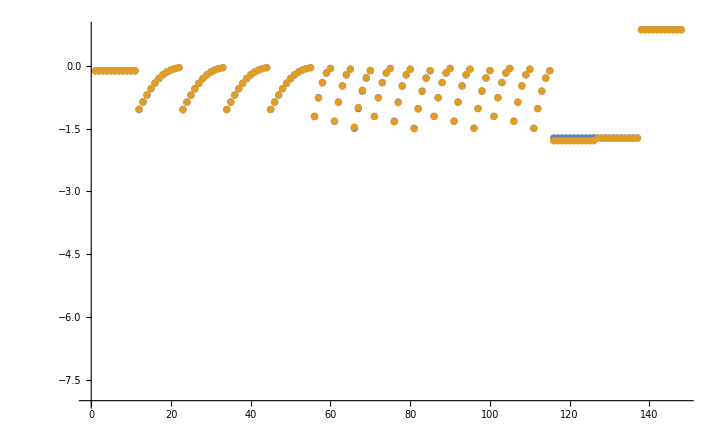

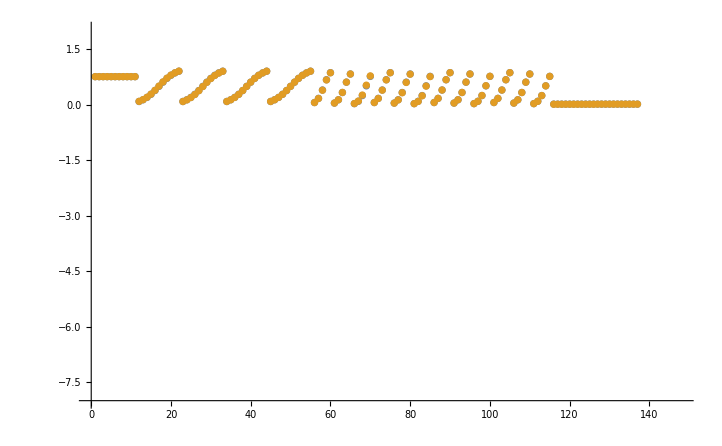

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

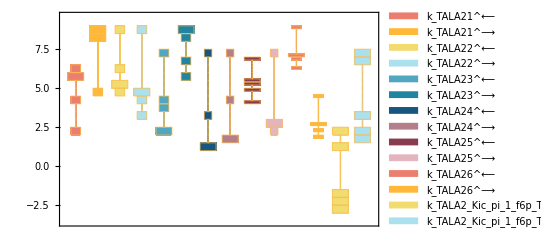

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

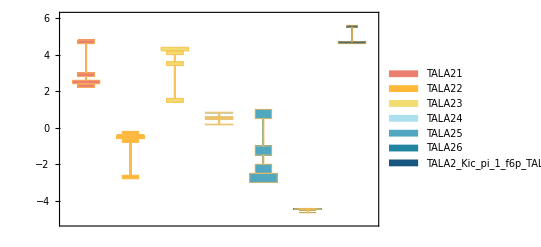

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

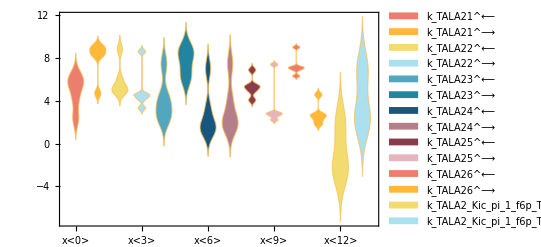

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

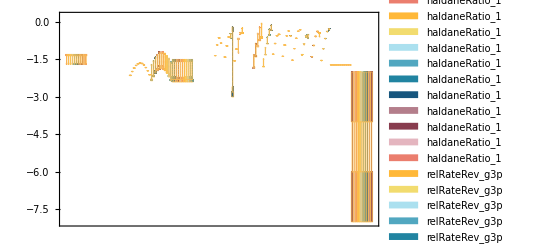

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateKcats[rxn, kcatList,absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
71.4 | 71.3955 | 0.00633007
79.4 | 71.3955 | 10.0813

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
125.79 | 125.79 | 2.31817×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138